# Cálculo de las secciones transversales de absorción, esparcimiento y extinción

```mathematica
Needs["MaTeX`"]
```

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
vlight=3*^17 ;(*nm s^-1*)
ϵ0=8.854187812*10^(-3)(*F/nm*);
```

Definiendo los factores de depolarización considerando los casos para un elipsoide oblato (a=b) L1= L2 y uno prolato (b=c) L2=L3

```mathematica
elipsoblato[a_,b_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1,L2,L3},
							L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L2=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2);
							L3=1-2 L1;
{L1,L2,L3}]
```

```mathematica
elipsprolato[a_,b_,c_]:=Module[{eab2=1-(b^2/a^2),L1,L2,L3},
							L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])]);
							L2=0.5*(1-L1);
							L3=0.5*(1-L1);{L1,L2,L3}];
```

```mathematica
factgeom[j_,a_,b_,c_]:=Which[a==b==c,1/3,a==b ,elipsoblato[a,b,c][[j]],
							b==c ,elipsprolato[a,b,c][[j]]]
```

```mathematica
factgeom[1,30.2,10,10]
```

0.107827

```mathematica
(*COMPROBANDO FUNCIONAMIENTO DE LOS FACTORES PARA OBLATO Y PROLATO*)
```

```mathematica
L1[a_,b_]:=Module[{eab2=1-(b^2/a^2),L1},L1=((1-eab2)/eab2) (-1+(1/(2*Sqrt[eab2])) Log[(1+Sqrt[eab2])/(1-Sqrt[eab2])])]
L11[a_,c_]:=Module[{eac2=1-(c^2/a^2),gac=((1-(1-(c^2/a^2)))/(1-(c^2/a^2)))^(1/2),L1},L1=(gac/(2 (eac2))) (π/2-ArcTan[gac])-(((gac)^2)/2)]
```

```mathematica
hola=Table[{Sqrt[1-(c^2/10^2)],L11[10,c]},{c,0.001,10,0.01}];
hola2=Table[{Sqrt[1-(b^2/10^2)],L1[10,b]},{b,0.001,10,0.01}];
```

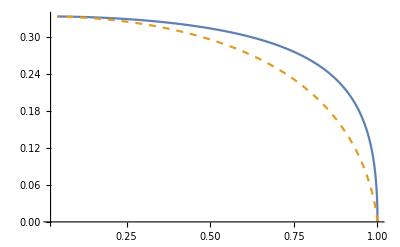

```mathematica
ListLinePlot[{hola,Style[hola2,Dashed]},PlotRange->All]
```

## Definiciones

### Función dieléctrica de tipo Drude

Definiendo la sección transversal de absorción

```mathematica
Cabs[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2 αx+αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Csca[a_,b_,c_,nm_,λ_,λp_,γ_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=1-((2 Pi vlight/λp)^2/((2 Pi vlight/λ)((2 Pi vlight/λ)+ I γ)));
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αx]^2/(6 Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cext[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[1]]+Cabs[a,b,c,nm,λ,λp,γ][[1]]
Cextx[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[2]]+Cabs[a,b,c,nm,λ,λp,γ][[2]]
Cextz[a_,b_,c_,nm_,λ_,λp_,γ_]:=Csca[a,b,c,nm,λ,λp,γ][[3]]+Cabs[a,b,c,nm,λ,λp,γ][[3]]
```

### Datos experimentales

```mathematica
Cabsexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Cabs,Cabsx,Cabsz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Cabs=k Im[2αx+ αz]/3;
										Cabsx=k Im[αx];
										Cabsz=k Im[αz];
										{Cabs,Cabsx,Cabsz}]
```

```mathematica
Cscaexp[a_,b_,c_,nm_,λ_,np_]:=Module[{ϵp,ϵm,k,αx,αz,Csca,Cscax,Cscaz},
										ϵm=nm^2;
										k=(2 Pi nm/λ);
										ϵp=np^2;
										αx=4 π a b^2  ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[1,a,b,c] (ϵp-ϵm)));
										αz=4 π a b^2 ((ϵp-ϵm)/ (3 ϵm + 3*factgeom[3,a,b,c](ϵp-ϵm)));
										Csca=k^4 Norm[2 αx+ αz]^2/(18 Pi);
										Cscax=k^4 Norm[αx]^2/(6 Pi);
										Cscaz=k^4 Norm[αz]^2/(6Pi);
										{Csca,Cscax,Cscaz}]
```

```mathematica
Cextexp[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[1]]+Cabsexp[a,b,c,nm,λ,np][[1]]
Cextexpx[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[2]]+Cabsexp[a,b,c,nm,λ,np][[2]]
Cextexpz[a_,b_,c_,nm_,λ_,np_]:=Cscaexp[a,b,c,nm,λ,np][[3]]+Cabsexp[a,b,c,nm,λ,np][[3]]
```

```mathematica
Cextexp[30,10,10,1.33,144,1]
```

66.7352

## Cálculos

### Datos experimentales

#### Aluminio

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
alum=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Aluminio Rakic.csv"];
```

```mathematica
alum1=Drop[Drop[alum,{208,415}],1];
λalum=alum1[[All,1]]*1000;
nalum=alum1[[All,2]];
alum2=Drop[alum,{1,209}];
kalum=alum2[[All,2]];
naluminio=nalum+ I kalum;
aluminio=Transpose[{λalum,naluminio}];
```

```mathematica
nindexalum=Interpolation[aluminio]
```

InterpolatingFunction[…]

```mathematica
h vlight/300
```

4.13567

Se graficará la Cext promedio contrastada con las Cext individuales

```mathematica
qextAlDrpromedio=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrx=Table[{h vlight/λ,Cextx[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
qextAlDrz=Table[{h vlight/λ,Cextz[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
```

```mathematica
h vlight/6
```

206.783

```mathematica
upperTicksCext=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorCext=Module[{labels,positions,size},labels={3.5,4.2,4.6,6,8,9,12,40};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

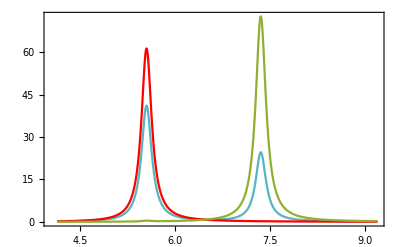

```mathematica
cextAl=ListLinePlot[{Style[qextAlDrpromedio,RGBColor[0.349,0.71,0.749]],Style[qextAlDrx,Red],Style[qextAlDrz,RGBColor[0.560181,0.691569,0.194885]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [eV]"],Magnification->1.5],Style[MaTeX["\lambda[nm]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["\langle C_{ext}"],MaTeX["C_{ext}^{(1)}"],MaTeX["C_{ext}^{(3)}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.55,0.65}]]
```

```mathematica
Export["CextAlbueno.svg",cextAl]
```

CextAlbueno.svg

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAlDr=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl1Dr=Table[{h vlight/λ,Cext[1.75,1.75,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl2Dr=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
qextAl3Dr=Table[{h vlight/λ,Cext[2.25,2.25,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];qextEsferaDr=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,125,350,0.01}];
```

```mathematica
h vlight/10
```

124.07

```mathematica
upperTicksAl=Module[{labels,positions},labels={124,138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

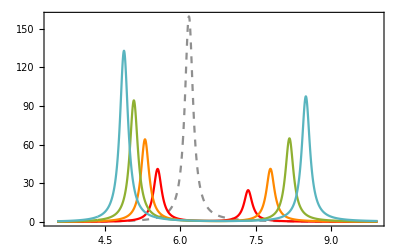

```mathematica
alc=ListLinePlot[{Style[qextEsferaDr,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlDr,Red],Style[qextAl1Dr,RGBColor[1,0.533,0]],Style[qextAl2Dr,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3Dr,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [eV]"],Magnification->1.5],Style[MaTeX["\lambda[nm]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
(*Export["Alc.pdf",alc]
```

#### Misma razón de aspecto

```mathematica
qextAlAR=Table[{h vlight/λ,Cext[1.0,1.0,0.5,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl1AR=Table[{h vlight/λ,Cext[1.5,1.5,0.75,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl2AR=Table[{h vlight/λ,Cext[2.0,2.0,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3AR=Table[{h vlight/λ,Cext[2.5,2.5,1.25,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
qextAl3sphere=Table[{h vlight/λ,Cext[2.0,2.0,2.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,130,350,0.01}];
```

```mathematica
h vlight/200
```

6.2035

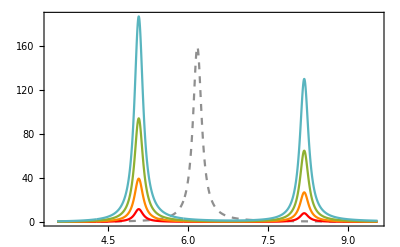

```mathematica
alAR=ListLinePlot[{Style[qextAl3sphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAlAR,Red],Style[qextAl1AR,RGBColor[1,0.533,0]],Style[qextAl2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAl3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [eV]"],Magnification->1.5],Style[MaTeX["\lambda[nm]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinorCext,upperTicksCext]}},PlotRange->All]
```

```mathematica
Export["AlAR.svg",alAR]
```

AlAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAlcont=Table[{h vlight/λ,Cabs[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.01}];
qscaAlcont=Table[{h vlight/λ,Csca[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ][[1]]},{λ,135,300,0.01}];
qextAlcont=Table[{h vlight/λ,Cext[1.5,1.5,1.0,1.33,λ,h vlight/(13.142),0.197/ℏ]},{λ,135,300,0.01}];
```

```mathematica
h vlight/9
```

137.856

```mathematica
upperTicksAl=Module[{labels,positions},labels={138,155,177,206,248,310};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAl=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

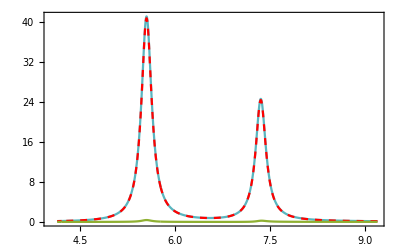

```mathematica
alcont=ListLinePlot[{Style[qextAlcont,RGBColor[0.349,0.71,0.749]],Style[qabsAlcont,Red,Dashed],Style[qscaAlcont,RGBColor[0.560181,0.691569,0.194885]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [nm^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [eV]"],Magnification->1.5],Style[MaTeX["\lambda[nm]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAl,upperTicksAl]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["C_{ext}"],MaTeX["C_{abs}"],MaTeX["C_{sca}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["AlContribuciones3.svg",alcont]
```

AlContribuciones3.svg

### Oro

Datos obtenidos de Johnson & Christy  DOI: https://doi.org/10.1103/PhysRevB.6.4370

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau11=Drop[Drop[au,{51,101}],1];
kau11=Drop[au,{1,52}];
λAu1=nau11[[All,1]]*1000; (*λ en nm*)
nau1=nau11[[All,2]];
kAu1=kau11[[All,2]];
nAu1=nau1+ I kAu1;
aU1=Transpose[{λAu1,nAu1}];
```

```mathematica
nindexau1=Interpolation[aU1];
```

```mathematica
300/(2*Pi*1.33)
```

35.8996

```mathematica
λAu1
```

{187.9,191.6,195.3,199.3,203.3,207.3,211.9,216.4,221.4,226.2,231.3,237.1,242.6,249.,255.1,261.6,268.9,276.1,284.4,292.4,300.9,310.7,320.4,331.5,342.5,354.2,367.9,381.5,397.4,413.3,430.5,450.9,471.4,495.9,520.9,548.6,582.1,616.8,659.5,704.5,756.,821.1,892.,984.,1088.,1216.,1393.,1610.,1937.}

#### Elipsoide oblato

#### Cambiando el tamaño de a

```mathematica
qextAu1c=Table[{h vlight/λ,Cextexp[15,15,10,1.33,λ,nindexau1[λ]]},{λ,190,1600}];
qextAu2c=Table[{h vlight/λ,Cextexp[17.5,17.5,10,1.33,λ,nindexau1[λ]]},{λ,190,1600}];
qextAu3c=Table[{h vlight/λ,Cextexp[20,20,10,1.33,λ,nindexau1[λ]]},{λ,190,1600}];
qextAu4c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]]},{λ,190,1600}];
qextAuEsferac=Table[{h vlight/λ,Cextexp[20,20,20,1.33,λ,nindexau1[λ]]},{λ,190,1600}];
qscaAu4c=Table[{h vlight/λ,Cscaexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,190,1600}];
qabsAu4c=Table[{h vlight/λ,Cabsexp[2.25,2.25,1.0,1.33,λ,nindexau1[λ]][[1]]},{λ,190,1600}];
```

```mathematica
h vlight/300
```

4.13567

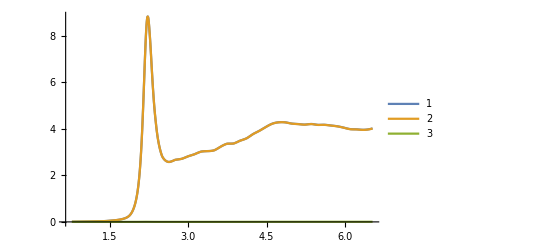

```mathematica
ListLinePlot[{qextAu4c,qabsAu4c,qscaAu4c},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

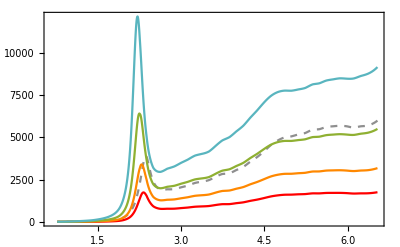

```mathematica
au1c=ListLinePlot[{Style[qextAuEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAu1c,Red],Style[qextAu2c,RGBColor[1,0.533,0]],Style[qextAu3c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu4c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.7}]]
```

```mathematica
Export["Auc.svg",au1c]
```

Auc.svg

#### Misma razón de aspecto

```mathematica
qextAuAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAu3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexau1[λ]]},{λ,300,800}];
qextAuEsferaAR=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
upperTicks4=Module[{labels,positions},labels={310,355,414,496,620,827,1240};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

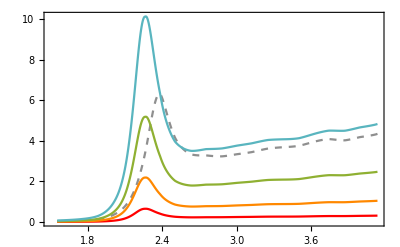

```mathematica
au1AR=ListLinePlot[{Style[qextAuEsferaAR,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAuAR,Red],Style[qextAu1AR,RGBColor[1,0.533,0]],Style[qextAu2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAu3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{All,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["a=20"],MaTeX["a=10 "],MaTeX["a=15"],MaTeX["a=20"],MaTeX["a=25"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["AuAR.svg",au1AR]
```

AuAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAucont=Table[{λ,Cabsexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qscaAucont=Table[{λ,Cscaexp[2,2,1,1.33,λ,nindexau1[λ]][[1]]},{λ,300,800}];
qextAucont=Table[{λ,Cextexp[2,2,1,1.33,λ,nindexau1[λ]]},{λ,300,800}];
```

```mathematica
h vlight/500
```

2.4814

```mathematica
upperTicks4=Module[{labels,positions},labels={0.8,0.85,0.9,0.95,1,1.1,1.2,1.3,1.4,1.5,1.7,2,2.3,2.5,3.1,4};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinor4=Module[{labels,positions,size},labels={0.8,0.85,0.95,1.15,1.25,1.35,1.45,1.55,1.6,1.65,1.75,1.85,2.1,2.3,2.6,2.8};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

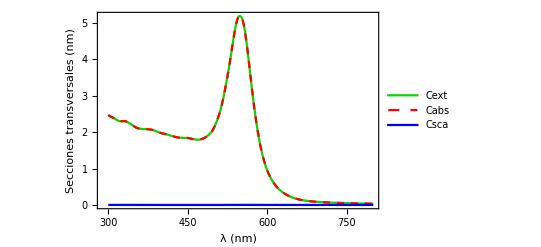

```mathematica
aucont=ListLinePlot[{Style[qextAucont,RGBColor[0.071,0.82,0]],Style[qabsAucont,Red,Dashed],Style[qscaAucont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinor4,upperTicks4]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AuContribuciones1.pdf",aucont]
```

### Plata

Datos obtenidos de Rakic.b4  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
ag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Plata Johnson.csv"];
```

```mathematica
nag1=Drop[Drop[ag,{51,101}],1];
kag1=Drop[ag,{1,52}];
λAg=nag1[[All,1]]*1000;(*λ en nm*)
nAg=nag1[[All,2]];
kAg=kag1[[All,2]];
nAgg=nAg+ I kAg;
plata=Transpose[{λAg,nAgg}];
```

```mathematica
nindexplata=Interpolation[plata];
```

#### Oblato

```mathematica
qextAgc=Table[{h vlight/λ,Cextexp[15,15,10,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg1c=Table[{h vlight/λ,Cextexp[17.5,17.5,10,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg2c=Table[{h vlight/λ,Cextexp[20,20,10,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAg3c=Table[{h vlight/λ,Cextexp[22.5,22.5,10,1.33,λ,nindexplata[λ]]},{λ,300,550}];
qextAgEsferac=Table[{h vlight/λ,Cextexp[2.0,2.0,2.0,1.33,λ,nindexplata[λ]]},{λ,300,550}];
```

```mathematica
h vlight/2.5
```

496.28

```mathematica
upperTicksAg=Module[{labels,positions},labels={310,355,414,496};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

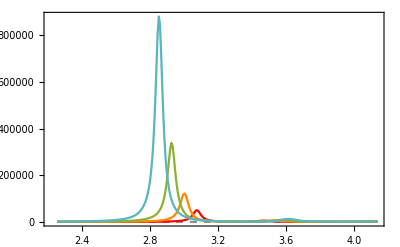

```mathematica
plata1c=ListLinePlot[{Style[qextAgEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgc,Red],Style[qextAg1c,RGBColor[1,0.533,0]],Style[qextAg2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["\mbox{AR}=1"],MaTeX["\mbox{AR}=1.5"],MaTeX["\mbox{AR}=1.75"],MaTeX["\mbox{AR}=2"],MaTeX["\mbox{AR}=2.25"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["Agc.svg",plata1c]
```

Agc.svg

#### Misma razón de aspecto

```mathematica
qextAgAR=Table[{h vlight/λ,Cextexp[1.0,1.0,0.5,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,0.75,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexplata[λ]]},{λ,300,500}];
qextAg3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexplata[λ]]},{λ,300,500}];
```

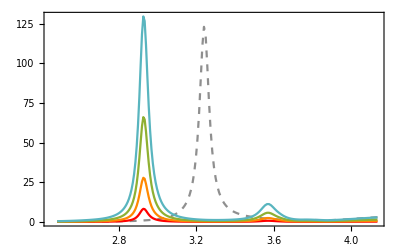

```mathematica
ag1AR=ListLinePlot[{Style[qextAg3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextAgAR,Red],Style[qextAg1AR,RGBColor[1,0.533,0]],Style[qextAg2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextAg3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\:\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\:\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\:\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["a=20\:\mbox{nm}"],MaTeX["a=10\:\mbox{nm} "],MaTeX["a=15\:\mbox{nm}"],MaTeX["a=20\:\mbox{nm}"],MaTeX["a=25\:\mbox{nm}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.85,0.65}]]
```

```mathematica
Export["AgAR.svg",ag1AR]
```

AgAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsAgcont=Table[{λ,Cabsexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qscaAgcont=Table[{λ,Cscaexp[15,15,1,1.33,λ,nindexplata[λ]][[1]]},{λ,750,950}];
qextAgcont=Table[{λ,Cextexp[15,15,1,1.33,λ,nindexplata[λ]]},{λ,750,950}];
```

```mathematica
h vlight/950
```

1.306

```mathematica
upperTicksAg=Module[{labels,positions},labels={1.3,1.34,1.37,1.4,1.45,1.5,1.55,1.6,1.65};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorAg=Module[{labels,positions,size},labels={1.31,1.32,1.33,1.35,1.38,1.43,1.48,1.5,1.53,1.63};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

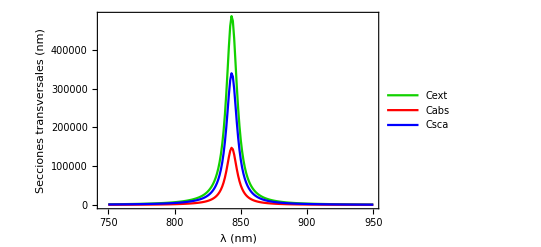

```mathematica
agcont=ListLinePlot[{Style[qextAgcont,RGBColor[0.071,0.82,0]],Style[qabsAgcont,Red],Style[qscaAgcont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["AgContribuciones3.pdf",agcont]
```

### Bismuto

Datos obtenidos de Hagemann  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
bism=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Bismuto Hagemann.csv"];
```

```mathematica
nbism1=Drop[Drop[bism,{152,303}],1];
kbism1=Drop[bism,{1,153}];
λBism=nbism1[[All,1]]*1000;(*λ en nm*)
nBis=nbism1[[All,2]];
kBis=kbism1[[All,2]];
nBismuto=nBis+ I kBis;
bismuto=Transpose[{λBism,nBismuto}];
```

```mathematica
nindexbismuto=Interpolation[bismuto];
```

```mathematica
10/(2*Pi*1.33)
```

1.19665

```mathematica
λBism
```

#### Oblato

```mathematica
qextBic=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBiEsferac=Table[{h vlight/λ,Cextexp[2.25,2.25,2.25,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
```

```mathematica
h vlight/0.1
```

12407.

```mathematica
h vlight/80
```

15.5088

```mathematica
upperTicksBi=Module[{labels,positions},labels={15,21,31,62};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorBi=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

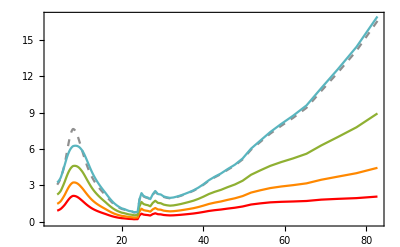

```mathematica
Bismuto1c=ListLinePlot[{Style[qextBiEsferac,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBic,Red],Style[qextBi1c,RGBColor[1,0.533,0]],Style[qextBi2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.15,0.7}]]
```

```mathematica
Export["Bic.svg",Bismuto1c]
```

Bic.svg

#### Misma razón de aspecto

```mathematica
qextBiAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
qextBi3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexbismuto[λ]]},{λ,15,300}];
```

```mathematica
h vlight/120
```

10.3392

```mathematica
1.75/2
```

0.875

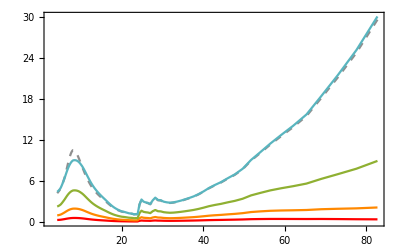

```mathematica
BismutoAR=ListLinePlot[{Style[qextBi3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextBiAR,Red],Style[qextBi1AR,RGBColor[1,0.533,0]],Style[qextBi2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextBi3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->{FontFamily->"CMU Serif",FontSize->20},FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorBi,upperTicksBi]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["a=2.5 \mbox{ nm}"],MaTeX["a=1 \mbox{ nm} "],MaTeX["a=1.5 \mbox{ nm}"],MaTeX["a=2 \mbox{ nm}"],MaTeX["a=2.5 \mbox{ nm}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.15,0.65}]]
```

```mathematica
Export["BisAR.svg",BismutoAR]
```

BisAR.svg

#### Para ver las contribuciones cambiando a

```mathematica
qabsBicont=Table[{λ,Cabsexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qscaBicont=Table[{λ,Cscaexp[2,2,0.5,1.33,λ,nindexbismuto[λ]][[1]]},{λ,10,500}];
qextBicont=Table[{λ,Cextexp[2,2,0.5,1.33,λ,nindexbismuto[λ]]},{λ,10,500}];
```

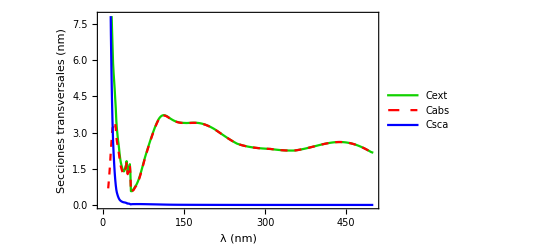

```mathematica
Bismutocont=ListLinePlot[{Style[qextBicont,RGBColor[0.071,0.82,0]],Style[qabsBicont,Red,Dashed],Style[qscaBicont,Blue]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style["Secciones transversales (nm)",Black,12],None},{Style["λ (nm)",Black,12],Style["ℏω (eV)",Black,12]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorAg,upperTicksAg]}},PlotLegends->Placed[LineLegend[{Style[#,FontFamily->"Times",10]&/@{"Cext","Cabs", "Csca"}},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),Spacings->0.15,LegendMarkerSize->15],{0.85,0.75}]]
```

```mathematica
(*Export["BiContribuciones1.pdf",Bismutocont]
```

## Óxido de magnesio

Datos obtenidos de Stephens and Malitson  DOI: http://dx.doi.org/10.1063/1.370750

```mathematica
mgO=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Óxido de magnesio Stephens.csv"];
```

```mathematica
mgO1=Drop[mgO,1];
λMgO=mgO1[[All,1]]*1000 ;(*λ en nm*)
nMgO=mgO1[[All,2]];
nmgo=Transpose[{λMgO,nMgO}];
```

```mathematica
nindexMgO=Interpolation[nmgo];
```

```mathematica
λMgO
```

{0.36,0.4104,0.4608,0.5112,0.5616,0.612,0.6624,0.7128,0.7632,0.8136,0.864,0.9144,0.9648,1.015,1.066,1.116,1.166,1.217,1.267,1.318,1.368,1.418,1.469,1.519,1.57,1.62,1.67,1.721,1.771,1.822,1.872,1.922,1.973,2.023,2.074,2.124,2.174,2.225,2.275,2.326,2.376,2.426,2.477,2.527,2.578,2.628,2.678,2.729,2.779,2.83,2.88,2.93,2.981,3.031,3.082,3.132,3.182,3.233,3.283,3.334,3.384,3.434,3.485,3.535,3.586,3.636,3.686,3.737,3.787,3.838,3.888,3.938,3.989,4.039,4.09,4.14,4.19,4.241,4.291,4.342,4.392,4.442,4.493,4.543,4.594,4.644,4.694,4.745,4.795,4.846,4.896,4.946,4.997,5.047,5.098,5.148,5.198,5.249,5.299,5.35,5.4}

#### Oblato

```mathematica
qextMgOc=Table[{h vlight/λ,Cextexp[1.5,1.5,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1c=Table[{h vlight/λ,Cextexp[1.75,1.75,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2c=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3c=Table[{h vlight/λ,Cextexp[2.25,2.25,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgOcsphere=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

```mathematica
h c/1200
```

1.03392

```mathematica
upperTicksMgO=Module[{labels,positions},labels={1,1.2,1.5,2.1,3.1,6.2};
positions=h vlight/#&/@labels;
Transpose[{positions,labels}]];
upperTicksMinorMgO=Module[{labels,positions,size},labels={};
positions=h vlight/#&/@labels;
labels=""&/@Range[Length[labels]];
size={-0.005,0}&/@Range[Length[labels]];
Transpose[{positions,labels,size}]];
```

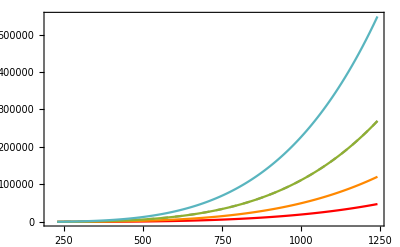

```mathematica
MgO1=ListLinePlot[{Style[qextMgOcsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOc,Red],Style[qextMgO1c,RGBColor[1,0.533,0]],Style[qextMgO2c,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3c,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["AR=1"],MaTeX["AR=1.5"],MaTeX["AR=1.75"],MaTeX["AR=2"],MaTeX["AR=2.5"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.15,0.65}]]
```

```mathematica
Export["MgOc.svg",MgO1]
```

MgOc.svg

```mathematica
qextMgOAR=Table[{h vlight/λ,Cextexp[1.0,1.0,.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO1AR=Table[{h vlight/λ,Cextexp[1.5,1.5,.75,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO2AR=Table[{h vlight/λ,Cextexp[2.0,2.0,1.0,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3AR=Table[{h vlight/λ,Cextexp[2.5,2.5,1.25,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
qextMgO3ARsphere=Table[{h vlight/λ,Cextexp[2.5,2.5,2.5,1.33,λ,nindexMgO[λ]]},{λ,1,5.4,0.01}];
```

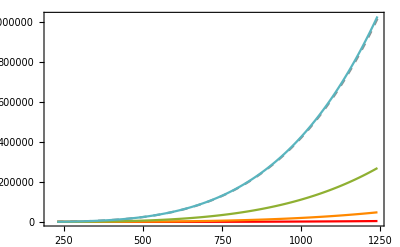

```mathematica
MgO2=ListLinePlot[{Style[qextMgO3ARsphere,Dashed,RGBColor[0.561,0.561,0.561]],Style[qextMgOAR,Red],Style[qextMgO1AR,RGBColor[1,0.533,0]],Style[qextMgO2AR,RGBColor[0.560181,0.691569,0.194885]],Style[qextMgO3AR,RGBColor[0.349,0.71,0.749]]},Frame->True,FrameStyle->Directive[Black,FontFamily->"Times",10],
FrameLabel->{{Style[MaTeX["C_{ext} [\mbox{nm}^2]"],Magnification->1.5],None},{Style[MaTeX["\hbar\omega [\mbox{eV}]"],Magnification->1.5],Style[MaTeX["\lambda[\mbox{nm}]"],Magnification->1.5]}},LabelStyle->Directive[Black, 15],FrameTicks->{{Automatic,None},{Automatic,Join[upperTicksMinorMgO,upperTicksMgO]}},PlotRange->All,PlotLegends->Placed[LineLegend[{Style[#,"CMU Serif",FontSize->20]&/@{MaTeX["a=2.5 \mbox{ nm}"],MaTeX["a=1 \mbox{ nm} "],MaTeX["a=1.5 \mbox{ nm}"],MaTeX["a=2 \mbox{ nm}"],MaTeX["a=2.5 \mbox{ nm}"]}},LegendMarkerSize->15,LegendMargins->-0.1,Spacings->0.05],{0.15,0.65}]]
```

```mathematica
Export["MgOAR.svg",MgO2]
```

MgOAR.svg

## Eritrocitos

```mathematica
RBCreal=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NRealRBC.csv"];
RBCimag=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\NImagRBC.csv"];
```

```mathematica
λRBC=RBCreal[[All,1]];
nRBC=RBCreal[[All,2]];
kRBC=RBCimag[[All,2]];
nindRBC=nRBC+ I kRBC;
RBC=Transpose[{λRBC,nindRBC}];
```

```mathematica
nindexRBC=Interpolation[RBC];
```

```mathematica
qabsRBC=Table[{λ,Cabsexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qscaRBC=Table[{λ,Cscaexp[20,20,12,1.33,λ,nindexRBC[λ]][[1]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexp[20,20,12,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpx[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
qextRBC=Table[{λ,Cextexpz[6,6,2,1.33,λ,nindexRBC[λ]]},{λ,400,600}];
```

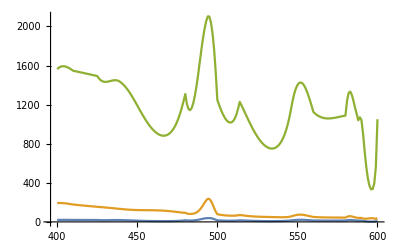

```mathematica
ListLinePlot[{qextRBC,qscaRBC,qabsRBC}]
```